```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/benjamin/Dokumente/Programme/stripey square

```mathematica
γ[x_,y_]:=0.5*(Cos[x]+Cos[y]);
A[x_,y_]:=1;
B[x_,y_]:=γ[x,y];
ϵ[x_,y_]:=4*Sqrt[A[x,y]^2-B[x,y]^2];
```

```mathematica
n=32;
numeric=Import["eigenvalues.dat","Data"];
justenergies=Table[numeric[[i]][[2]],{i,1,Length[numeric]}];
analytic=Table[{ϵ[x*2*π/n,y*2*π/n],ϵ[x*2*π/n,y*2*π/n]},{x,0,n-1},{y,0,n-1}];
```

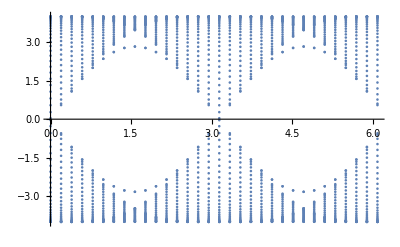

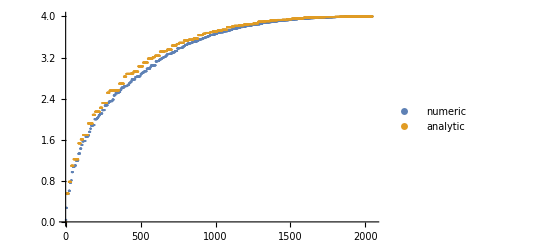

```mathematica
ListPlot[numeric]
ListPlot[{Sort[Flatten[Abs[justenergies]]],Sort[Flatten[analytic]]},PlotLegends->{"numeric","analytic"}]
```